# Математические модели динамики численности одного вида

## Задание 1. Модель Мальтуса.

Простейшая модель численности популяции одного вида . Характеристики :
1. Популяция больших размеров (численность измеряется миллионами).
2. Не существует факторов сдерживания роста популяции:
	1) Болезни;
	2) Хищники;
	3) Конкурирующие виды;
	4) Ограниченность питания и др.
3. Пренебрегаем процессами иммиграции и эммиграции.
4. Случайные различия между различными особями игнорируются.
5. Каждая особь имеет равные шансы родиться и умереть с течением времени.

Концепция:
1. Численность популяции - это непрерывная функция от времени N(t).
2. Рождаемость и смертность непрерывны во времени и заданы коэффициентами на одну особь в единицу времени.
3. N’(t) = (a - b) * N(t).
4. N(t0) = N0.

#### 1.1

-Graphics-

```mathematica
ClearAll[t0,N0];
sol=DSolveValue[{NN'[t]==(α-β)NN[t],NN[t0]==N0},NN[t],t]
```

ⅇ^(t α-t0 α-t β+t0 β) N0

```mathematica
getMaltusSolution[α_,β_,N0_,t0_]:=N0*Exp[(α-β)(t-t0)]
```

#### 1.2

```mathematica
ClearAll[t0,N0,sol];
t0=0;
N0=10;
sol=getMaltusSolution[α,β,N0,t0]
```

10 ⅇ^(t (α-β))

```mathematica
funcs=(sol/.#)&/@{{α->0,β->2},{α->2,β->2},{α->2,β->0}}
```

{10 ⅇ^(-2 t),10,10 ⅇ^(2 t)}

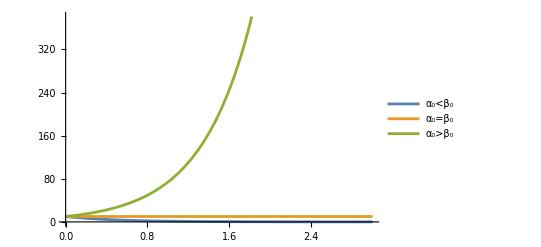

```mathematica
Plot[funcs,{t,t0,3},PlotLegends->{"α_0<β_0","α_0=β_0","α_0>β_0"}]
```

#### 1.3

При t -> ∞ для ...
	 1) случаю, когда коэффициенты рождаемости и смертности совпадают, решением будет константа N0, значит N’(t) = 0, нет ни роста, ни падения численности. Поведение такого решения неизменно.
	2) для случая, когда коэффициент рождаемости больше, чем коэффициент смертности, решением будет экспоненциальная функция e^t. Будет наблюдаться экспоненциальный рост численности населения.
	3) для случая, когда коэффициент рождаемости меньше, чем коэффициент смертности, решением будет e^-t, что означает экспоненциальное убывание численности населения. Если брать во внимание предельное значение решения, можно сказать, что популяция вымрет.

Устойчивость решения относится к поведению решения в ответ на малые изменения входных данных или начальных условий. Положение равновесия, соответствующее решению модели при совпадении коэффициентов рождаемости и смертности неустойчиво. Это видно из графиков.
	В отличие от положения равновесия N(t) = 0, оно является устойчивым для случая, когда рождаемость меньше смертности.

#### 1.4

1) Коэффициент рождаемости меньше коэффициента смертности.

```mathematica
α=1;
β=2;
```

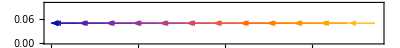

```mathematica
StreamPlot[{(α-β)x,0},{x,0,3},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

2) Коэффициент рождаемости совпадает с коэффициентом смертности.

```mathematica
α=1;
β=1;
```

```mathematica
StreamPlot[{(α-β)x,0},{x,0,3},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

-Graphics-

3) Коэффициент рождаемости больше коэффициента смертности.

```mathematica
α=2;
β=1;
```

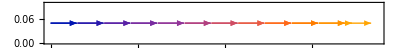

```mathematica
StreamPlot[{(α-β)x,0},{x,0,3},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

В случаях 2), 3) все близкие траектории в фазовом пространстве стремятся не к положению равновесия или траектории со временем. Cистема не стабилизируется вокруг этого положения равновесия.

В случае 1), N = 0 будет положением равновесия при α < β, к нему стремятся траектории, определение удовлетворено.

## Задание 2. Модель Ферхюльста.

Сдерживающим фактором является ограниченность ресурсов.
	Np - это равновесная численность популяции, которую может обеспечить окружающая среда.

#### 2.1

```mathematica
-Graphics-
-Graphics-
```

-Graphics-

-Graphics-

```mathematica
ClearAll[t0,N0];
sol=DSolveValue[{NN'[t]==NN[t]*k(1-NN[t]/Np),NN[t0]==N0},NN[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(3^t N0 Np)/(3^t N0-3^t0 N0+3^t0 Np)

```mathematica
getFerhulstSolution[k_,Np_,N0_,t0_]:=(Np*N0)/(N0+(Np-N0)*Exp[k(t0-t)])
```

#### 2.2

```mathematica
ClearAll[t0,k,Np,sol];
t0=0;
k=5;
Np=10;
sol=getFerhulstSolution[k,Np,N0,t0]
```

(10 N0)/(ⅇ^(-5 t) (10-N0)+N0)

```mathematica
funcs=(sol/.#)&/@{{N0->1},{N0->10},{N0->20}}
```

{10/(1+9 ⅇ^(-5 t)),10,200/(20-10 ⅇ^(-5 t))}

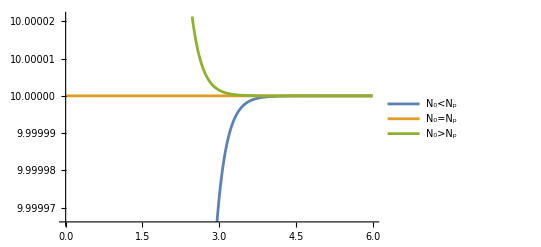

```mathematica
Plot[funcs,{t,t0,6},PlotLegends->{"N_0<N_p","N_0=N_p","N_0>N_p"}]
```

#### 2.3

При t -> ∞ наблюдается, что...
	1) для случая, когда N0 > Np выполняется свойство эффекта насыщения численности населения, то есть N(t) -> Np.
	2) то же свойство выполняется и для случая, когда начальная численность популяции N0 меньше, чем равновесная численность популяции Np. То есть коэффициент отклонения численности от равновесного значения как бы настраивает численность населения, корректируя ее с течением времени. Что в принципе и согласуется с нашим пониманием окружающего мира.
	3) В случае же, когда N0 = Np сразу можно сказать, что численность населения “настроена”. Причем такое положение равновесия является ассимптотически устойчивым, то есть даже при небольших различиях во входных данных, получим, что N(t) -> Np.
	Чем больше коэффициент k, тем быстрее численность населения стремится к Np.

#### 2.4

Сразу проиллюстрируем два случая, когда N0 > Np и N0 < Np.

```mathematica
ClearAll[t0,N0,k,Np];
t0=0;
k=10;
Np=2;
N0=5;
```

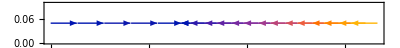

```mathematica
StreamPlot[{x*k(1-x/Np),t0},{x,0,N0},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

Положение равновесия N0 = Np является устойчивым. Это подтверждает как направление фазовых траекторий, так и результаты графического отображения всех случаев отношения N0 и Np. Рассмотрим положение равновесия N0 = 0:

```mathematica
ClearAll[t0,N0,k,Np];
t0=0;
k=10;
Np=2;
N0=0;
```

```mathematica
StreamPlot[{x*k(1-x/Np),t0},{x,0,N0},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

StreamPlot::plld: Endpoints for x in {x,0,0} must have distinct machine-precision numerical values.

StreamPlot[{x k (1-x/Np),t0},{x,0,N0},{y,0,0.1},AspectRatio→Automatic,ImageSize→{{300,500}}]

```mathematica
ClearAll[t0,k,Np];
t0=0;
k=5;
Np=0;
sol=getFerhulstSolution[k,Np,N0,t0]
funcs=(sol/.#)&/@{{N0->1},{N0->10},{N0->20}}
Plot[funcs,{t,t0,6},PlotLegends->{"N_0<N_p","N_0=N_p","N_0>N_p"}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

{Indeterminate,Indeterminate,Indeterminate}

-Graphics-

Из того, что я видел на графике, предположу, что N0 = 0 является устойчивым хотя и возможно математически неправильным.

#### 2.5

-Graphics-

```mathematica
ClearAll[t0,N0,k,Np,sol];
t0=0;
N0=Np/4;
t1=1;
N1=Np/2;
N2=3/4 Np;
```

```mathematica
Solve[N1==(Np*N0)/(N0+(Np-N0)*Exp[k(t0-t1)]),k,Reals]
```

{{k→Log[3]}}

```mathematica
k=Log[3];
Solve[N2==(Np*N0)/(N0+(Np-N0)*Exp[k(t0-t)]),t,Reals]
```

{{t→2}}

#### 3.1

```mathematica
-Graphics-
-Graphics-
```

-Graphics-

-Graphics-

```mathematica
ClearAll[α0,β0,N0,t,t0,α,β]
sol=DSolveValue[{NN'[t]==(α0*NN[t]-β0)NN[t],NN[t0]==N0},NN[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(ⅇ^(t0 β0) N0 β0)/(-ⅇ^(t β0) N0 α0+ⅇ^(t0 β0) N0 α0+ⅇ^(t β0) β0)

Рассмотри случай, когда N0 > Nкр = β_0/α_0. N0*α_0>β_0, при этом часть выражения в знаменателе может стать отрицательной и получится число очень близкое к 0. Найдем такое t при котором знаменательно обращается в 0:

```mathematica
ClearAll[α0,β0,N0,t,t0]
Solve[α0*N0+(β0-α0*N0)*Exp[β0(t-t0)]==0&&α0*N0>β0,t,Reals]
```

{{t→ConditionalExpression[(t0 β0+Log[(N0 α0)/(N0 α0-β0)])/β0, ]}}

Для случая, когда N0 = Nкр = β_0/α_0, решением будет само Nкр = β_0/α_0. В случае, если N0 < Nкр, все будет хорошо.
	При условии, что β_0=0 в решении будет неопределенность 0/0:

```mathematica
Limit[(β0*N0)/(α0*N0+(β0-α0*N0)*Exp[β0(t-t0)]),β0->0]
```

N0/(1+N0 (-t+t0) α0)

Это не правильно, так N(t) всегда будет отрицательным.

```mathematica
getNonLinearMaltusSolution[α0_,β0_,N0_,t0_]:=(β0*N0)/(α0*N0+(β0-α0*N0)*Exp[β0(t-t0)])
```

#### 3.2

```mathematica
ClearAll[α0,β0,N0,t,t0,α,β];
α0=3;
β0=12;
t0=0;
sol=getNonLinearMaltusSolution[α0,β0,N0,t0]
```

(12 N0)/(ⅇ^(12 t) (12-3 N0)+3 N0)

```mathematica
funcs=(sol/.#)&/@{{N0->1},{N0->4},{N0->5}}
```

{12/(3+9 ⅇ^(12 t)),4,60/(15-3 ⅇ^(12 t))}

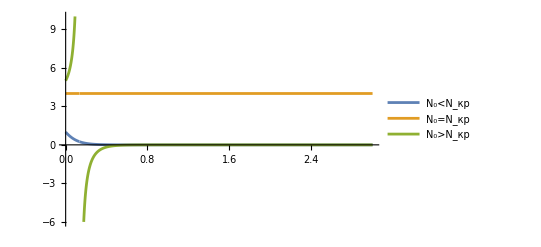

```mathematica
Plot[funcs,{t,t0,3},PlotLegends->{"N_0<N_(:043a:0440)","N_0=N_(:043a:0440)","N_0>N_(:043a:0440)"}]
```

#### 3.3

Сразу рассмотрим, когда N(t) -> к бесконечности. Ранее было получино такое выражение для t:

```mathematica
(t0 β0+Log[(N0 α0)/(N0 α0-β0)])/β0
```

1/12 Log[(3 N0)/(-12+3 N0)]

Проверим его для заданных значений:

```mathematica
ClearAll[α0,β0,N0,t,t0,α,β];
α0=3;
β0=12;
t0=0;
N0=5;
SuperStar[t]=(t0 β0+Log[(N0 α0)/(N0 α0-β0)])/β0//N
```

0.13412

Рассмотрим график ближе, чтобы убедиться:

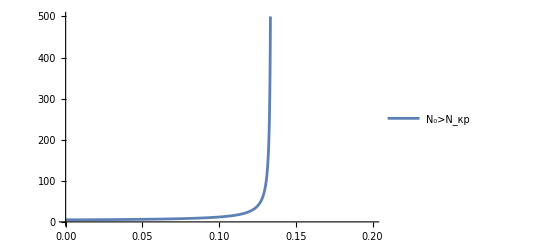

```mathematica
Plot[funcs[[3]],{t,t0,0.5},PlotLegends->{"N_0>N_(:043a:0440)"},PlotRange->{{0,0.2},{0,500}}]
```

Подсчеты были верны, t* также определено правильно. Что касается самого случая N0 > Nкр, решение строится только на промежутке [t0, t*] и можно наблюдать огромный рост значения N(t) за короткий промежуток времени для заданных параметров.
	Для случая N0 < Nкр наблюдаем монотонное убывание N(t) к 0 за небольшой промежуток времени. Для случая N0 = Nкр решение вырождается в константу, это положение равновесия не является устойчивым.

#### 3.4

```mathematica
ClearAll[α0,β0,N0,t,t0,α,β];
α0=3;
β0=12;
t0=0;
N0=1;
```

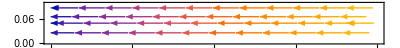

```mathematica
StreamPlot[{x(α0*x-β0),t0},{x,0,N0},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

```mathematica
ClearAll[α0,β0,N0,t,t0,α,β];
α0=3;
β0=12;
t0=0;
N0=5;
```

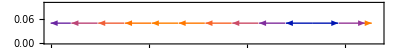

```mathematica
StreamPlot[{x(α0*x-β0),t0},{x,0,N0},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

Положение равновесия N = 0 будет устойчивым в случае, когда N0 < Nкр. N = Nкр устойчивым не является.